# Introduction to Mathematica: Session 3 Peter Manshausen 09/08/2017

```mathematica
f[x_]:= Exp[-x^2]
f'[x]
f''[x]
D[f[x],{x,5}]
```

-2 ⅇ^(-x^2) x

-2 ⅇ^(-x^2)+4 ⅇ^(-x^2) x^2

-120 ⅇ^(-x^2) x+160 ⅇ^(-x^2) x^3-32 ⅇ^(-x^2) x^5

```mathematica
Simplify[D[f[x],{x,5}]]
```

-8 ⅇ^(-x^2) x (15-20 x^2+4 x^4)

```mathematica
FullSimplify[D[f[x],{x,5}]]
```

-8 ⅇ^(-x^2) x (15+4 x^2 (-5+x^2))

```mathematica
Integrate[Sec[x],x]
Integrate[Sec[x],{x,0,1}]
```

-Log[Cos[x/2]-Sin[x/2]]+Log[Cos[x/2]+Sin[x/2]]

2 ArcTanh[Tan[1/2]]

```mathematica
NIntegrate[Sec[x],{x,0,1}, PrecisionGoal->10]
N[Integrate[Sec[x],{x,0,1}], 50]
```

1.22619

1.2261911708835170708130609674719067527242483502207

```mathematica
N[∫_0^1 Sec[x]ⅆx,58]
```

1.226191170883517070813060967471906752724248350220740279139

```mathematica
Integrate[Sec[x],{x,0,1.}]
```

1.22619

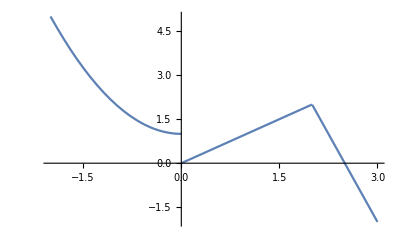

```mathematica
Plot[Piecewise[{{x^2+1, x⩽0}, {x,0⩽x<2}, {10-4 x, x⩾2}}], {x,-2,3}]
```

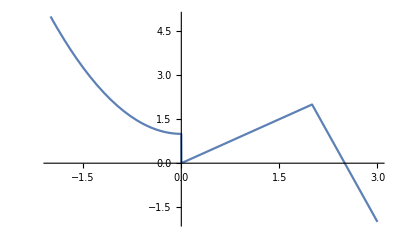

```mathematica
Plot[If[x<0,x^2+1, If [x<2, x,10-4 x ]],{x,-2,3}]
```

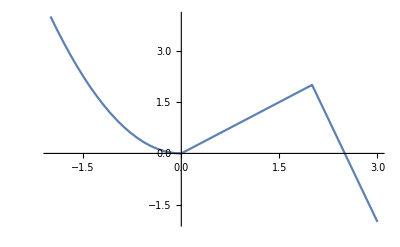

```mathematica
Plot[Which[x<0, x^2, 0<x<2, x, x>2, 10-4x], {x,-2,3}]
```

```mathematica
x=.
y=.
```

π/6

10

{x→InterpolatingFunction[{{0., 10.}}, <>],y→InterpolatingFunction[{{0., 10.}}, <>]}

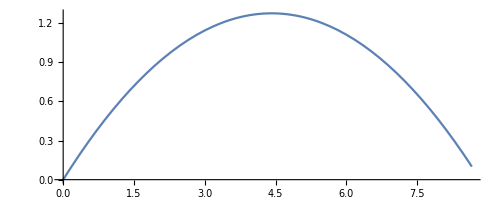

```mathematica
θ = Pi/6
v0=10
sol=NDSolve[
{y''[t]==-9.8, x''[t]==0,
x'[0]==v0* Cos[θ], y'[0]==v0 Sin[θ],
x[0]==0, y[0]==0},
 
{x,y}, {t,0,10}][[1]]
ParametricPlot[{x[t], y[t]}/.sol,{t,0,1}]
```

π/6

10

{y→Function[{t},(5.-4.9 t) t],x→Function[{t},8.66025 t]}

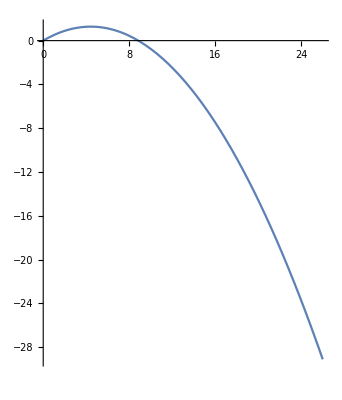

```mathematica
θ = Pi/6
v0=10
sol=DSolve[
{y''[t]==-9.8, x''[t]==0,
x'[0]==v0* Cos[θ], y'[0]==v0 Sin[θ],
x[0]==0, y[0]==0},
 
{x,y}, {t,0,10}][[1]]
ParametricPlot[{x[t], y[t]}/.sol,{t,0,3}]
```

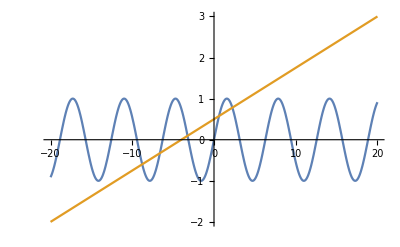

```mathematica
y1[x_]:=Sin[x];
y2[x_]:=(4+x)/8
Plot[{y1[x],y2[x]}, {x,-20,20}]
```

```mathematica
FindRoot[y1[x]-y2[x],{x,-3}]
```

{x→-3.2371}

```mathematica
Solve[2x+3y-z==-1 && x-6y+4z==7 && -6x-2y+2z==52, {x,y,z}]
```

{{x→-6,y→19/2,z→35/2}}

```mathematica
Solve[76.60 c+45.20b+23.10 m==1523.10&&30c+18b+12m==642&&c>0 &&b>0&&m>0,{c,b, m},Integers]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{c→13,b→4,m→15}}